```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
ufun=NDSolveValue[{-Laplacian[u[x,y],{x,y}]==10,
u[x,0]==0,u[x,1]==1},
u,{x,0,1},{y,0,1}];
Plot3D[ufun[x,y],{x,0,1},{y,0,1},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
ufun=NDSolveValue[{-Laplacian[u[x,y],{x,y}]==10,
u[x,0]==0,u[x,1]==1},
u,{x,0,1},{y,0,1}];
Plot3D[ufun[x,y],{x,0,1},{y,0,1},ColorFunction->"TemperatureMap"]
```

```mathematica
hyperbolicSol=NDSolveValue[{-Laplacian[u[x,y],{x,y}]==Sin[x+y],
u[x,0]==0,u[x,1]==1},
u,{x,0,1},{y,0,1}];
Plot3D[hyperbolicSol[x,y],{x,0,1},{y,0,1},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
Ω=ImplicitRegion[!((x-5)^2+(y-5)^2≤3^2),{{x,0,5},{y,0,10}}];
RegionPlot[Ω,AspectRatio->Automatic]
```

-Graphics-

```mathematica
op=-Laplacian[u[x,y],{x,y}]-Sin[x+y];
```

```mathematica
Subscript[Γ, D]={DirichletCondition[u[x,y]==0, x==0&&8≤y≤10],
DirichletCondition[u[x,y]==100,(x-5)^2+(y-5)^2==3^2]};
```

```mathematica
ufun=NDSolveValue[{op==0,Subscript[Γ, D]},u,{x,y}∈Ω]
```

InterpolatingFunction[…]

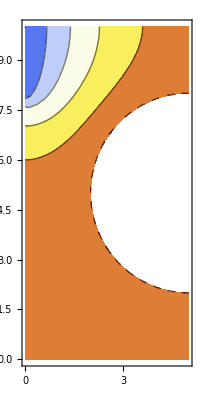

```mathematica
ContourPlot[ufun[x,y],{x,y}∈Ω,ColorFunction->"Temperature",AspectRatio->Automatic]
```

```mathematica
Plot3D[ufun[x,y],{x,0,1},{y,0,1},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
Ω=ImplicitRegion[!((x-5)^2+(y-5)^2≤3^2),{{x,0,5},{y,0,10}}];
op=-Laplacian[u[x,y],{x,y}]-Sin[x+y];
```

```mathematica
Subscript[Γ, N]=NeumannValue[-2u[x,y],((x-5)^2+(y-5)^2==3^2)];
```

```mathematica
Subscript[Γ, D]=DirichletCondition[u[x,y]==0, x==0&&8≤y≤10];
```

```mathematica
ufun=NDSolveValue[{op==Subscript[Γ, N],Subscript[Γ, D]},u,{x,y}∈Ω]
```

InterpolatingFunction[…]

```mathematica
Plot3D[ufun[x,y],{x,y}∈Ω]
```

-Graphics3D-

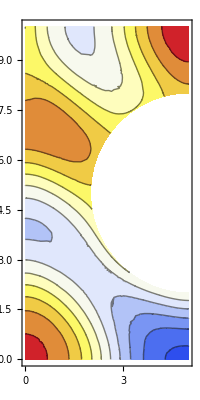

```mathematica
ContourPlot[ufun[x,y],{x,y}∈Ω,ColorFunction->"Temperature",AspectRatio->Automatic]
```